#### An attempt to apply classify

```mathematica
ExampleData[{"Text",""}];
```

```mathematica
{{"Text","AliceInWonderland"},{"Text","BeowulfModern"},{"Text","CodeOfHammurabiEnglish"},{"Text","DeclarationOfIndependence"},
{"Text","DonQuixoteIEnglish"},{"Text","FaustI"},{"Text","FederalistTen"},{"Text","FriendsRomansCountrymen"},{"Text","GenesisKJV"},{"Text","JFKInaugural"},{"Text","MagnaCarta"},{"Text","OnTheNatureOfThingsEnglish"},{"Text","OriginOfSpecies"},{"Text","PlatoMenoEnglish"},{"Text","PrideAndPrejudice"}}
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jamilya_bilyalova/Desktop/GitHub/Summer2018Starter/Project 2018

```mathematica
lines=Import["movie_lines.tsv","Text"];
```

```mathematica
list=StringSplit[lines,{"\t","\n"}];
```

```mathematica
list[[1;;20]]
```

{L1045,u0,m0,BIANCA,They do not!,L1044,u2,m0,CAMERON,They do to!,L985,u0,m0,BIANCA,I hope so.,L984,u2,m0,CAMERON,She okay?}

```mathematica
listOfLines=Partition[list,5][[All,-1]];
```

```mathematica
listOfLines[[3]]
```

I hope so.

```mathematica
StringContainsQ
```

StringContainsQ

```mathematica
questions=Select[listOfLines,StringContainsQ[#,"?"]&];
```

```mathematica
questions[[1;;200]];
```

```mathematica
normalLines=Complement[listOfLines,questions];
```

```mathematica
normalLines//Normal
```

{,*, *, * ,    *,1000 meters...,1002.,84371,Zowie.,Zowie...,ZURIA,ZYDOWSKI,$383.,$40 a day and expenses. Expenses run pretty high on a case like this. I'm a long way from home. I don't have a B.C. Licence. I'd need about $500 for a retainer.}
 |  |  |  |

```mathematica
questions//Normal
```

{She okay?,I'm kidding.  You know how sometimes you just become this ""persona""?  And you don't know how to quit?",Like my fear of wearing pastels?,What good stuff?,17212,Dance?,Wait here.  If you have to use this use it.  Don't choke. Okay?,What are you going to do?}
 |  |  |  |

```mathematica
questionsWithoutQuestion=StringReplace[questions,{"?"->"."}]
```

{She okay.,I'm kidding.  You know how sometimes you just become this ""persona"".  And you don't know how to quit.",Like my fear of wearing pastels.,What good stuff.,17212,Dance.,Wait here.  If you have to use this use it.  Don't choke. Okay.,What are you going to do.}
 |  |  |  |

```mathematica
questionsWithoutQuestion=StringReplace[questions,{"\""->""}]
```

{She okay.,I'm kidding.  You know how sometimes you just become this persona.  And you don't know how to quit.,Like my fear of wearing pastels.,What good stuff.,17212,Dance.,Wait here.  If you have to use this use it.  Don't choke. Okay.,What are you going to do.}
 |  |  |  |

```mathematica
questionsWithoutQuestion//Length
```

17219

Sentences | Class
normalLines[[50;;84384]] -> “Not Questions”
questionWithoutQuestions[[1;;17219]] -> “Questions”

```mathematica
normalLines//Normal
```

{,*, *, * ,    *,1000 meters...,1002.,84371,Zowie.,Zowie...,ZURIA,ZYDOWSKI,$383.,$40 a day and expenses. Expenses run pretty high on a case like this. I'm a long way from home. I don't have a B.C. Licence. I'd need about $500 for a retainer.}
 |  |  |  |

```mathematica
<|
```

```mathematica
cl=Classify[<|"not Q"->normalLines[[50;;150]],"questions"->questionsWithoutQuestion[[1;;100]]|>]
```

ClassifierFunction[…]

```mathematica
cl["I'm fine."]
```

not Q

```mathematica
testset=<|"not Q"->normalLines[[151;;250]],"questions"->questionsWithoutQuestion[[101;;200]]|>;
```

```mathematica
cm=ClassifierMeasurements[cl,testset]
```

ClassifierMeasurementsObject[…]

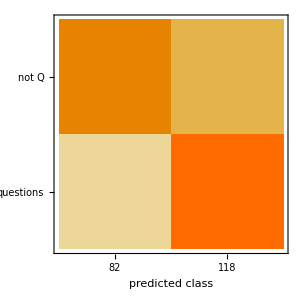

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
Table[1,84334]
```

{1,1}

```mathematica
Rule[a,1]
```

a→1

```mathematica
tra
```

```mathematica
Classify[
```

```mathematica
Table["Not Question",84334];
```

```mathematica
Association[MapThread[Rule,normalLines[[50;;84384]],Table["Not Question",84334]]]
```

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in ….

Association[MapThread[Rule,normalLines⟦50;;84384⟧,Table[1,84334]]]

```mathematica
Association[normalLines[[52;;90]]]
```

Association[normalLines⟦52;;90⟧]

```mathematica
normalLinesnobrackets=StringReplace[normalLines,{"""→""}]
```

```mathematica
Column@normalLines[[1;;50]]
```

*
 *
 * 
    *
1000 meters...
1002.
1062 Sherman Drive. Apartment 1E Rockville Center.
10%.  That's ...
1/16 tru' 'dat.  True 'dat.
1322 last year in LA county.  Up 26 percent from the year before.
1500 meters. We're getting too close...
1550 millibars dropping 20 MB per minute shit we're hemorrhaging air. <u>Somethin'</u> took a swipe at us.
15 6-gigs here...90 gigs total...other ship carries 20-gig cells so...five. Five total to launch.
15 sir.
1867.  Seward's Folly. We paid 7.2 million dollars for it. A tidy sum then as well as now. I'm quoting my father of course.
1959.
1ST MAN
1ST OFFICER
200-year-old single-malt scotch is to ""booze"" as foie gras is to ""duck guts."""
#21. Way behind schedule. It's top- secret but everybody knows it's a digital broadcast space. They see the dishes on top the fiber optics going in.
25 pounds or 25 pence in fours.
26 weeks.
2ND MAN
30 hours to Neptune orbit.
30 seconds...
32 feet six inches!
34000. But they're real short lines. 'Just came out that way.
350 pounds.
37 usages of Himbry  located in the registar's office. 9 Tatum's 47 Riley's. And that's just on campus. It's hopeless.
53!
53.
5-4-3-2-1-drop drop drop!
555-7600. Tell them it's a code dragonfly. They should get you through.
'57 1 believe--
5'7"" green eyes... long legs... great skin... perfect.."
60 years ago.
6... 5...
70 seconds! You still got 70 seconds to level this beast out!
79 kilos.
818-753-0088.
85000 dollars.
90 over 50 and falling... .
A .45--
Aaaaaaaaaa!
Aaa!  D'Artagnan!  These passages were constructed for the King's security not so you could step from my father's portrait and startle me to death!
Aaagh!
Aaagh! Rape!
Aaaww shit!... evil woman!
Aah!

```mathematica
data=ResourceData["Sample Data: Animal Weights"];
```

```mathematica
"jump*"
"jump"~~___
"c"~~__~~"ñ"~~___~~"n"
[{{"Dutch","Spanish"},"molecula"~~___}]
With IgnoreCasepaclet:ref/IgnoreCase->Truepaclet:ref/True lowercase and uppercase letters are treated as equivalent
StringMatchQ["acggtATTCaagc",__~~"aT"~~__,IgnoreCase->True]
StringPosition["abAB","a",IgnoreCase->True]
StringReplace["Abab","ab"->"xy",IgnoreCase->True]
WordFrequency["Buffalo from Buffalo, which buffalo from Buffalo bully, themselves bully buffalo from Buffalo.", "Buffalo",IgnoreCase->True]
StringReplace["abcd abcd","b"|"c"->"X"]
StringCases["abc abcb abdc","ab"~~_]
StringCases["abc abcb abdc","ab"~~x_->x]
StringCases["abbcbccaabbabccaa",x_~~x_]
StringReplace[{"abww","abc","abcd"},"b"~~__->"X"]
StringSplit["a--bbb---ccc--dddd","--"]
StringSplit["a bbb  cccc aa   d"](*b and everything after that*)
```

```mathematica
StringSplit["11a22b3",_?LetterQ]
```

{11,22,3}

You can use all the standard Wolfram Language pattern objects in string patterns. Single blanks (_) always stand for single characters. Double blanks (__) stand for sequences of one or more characters.

Sequence Learning and NLP with Neural Networks
The input to the net is a sequence of some kind
Create a class Encoder:
enc = NetEncoder[{“Class”, {“male”, “female”}}]
Convert female to class 2 and male to class 1
enc[{“male”, “female”, “female”}]

```mathematica
StringCountpaclet:ref/StringCount["s",patt]
```